```mathematica
mn = 0.939;

μ[mx_]:=mx/mn;
γ[ve_]:= 1/Sqrt[1 - ve^2]; (*natural units *)
p[ve_, mx_]:=γ[ve]*mx*ve*0.5;
s[mx_] :=(*2γ[0.6]*mx*mn+mx^2+mn^2;*)mx^2/μ[mx]^2*(1+μ[mx]^2+2/(√0.3)*μ[mx]);
Er[ctheta_,ve_, mx_]:= (mn*mx^2*γ[ve]^2*ve^2)/(mn^2 + mx^2 + 2*γ[ve]*mx*mn)*(1 - ctheta);
jacobioan[B_, mx_]:=B*((1+μ[mx]^2+2/(√B)*μ[mx])/(2*(1-B)*mx^2));
```

```mathematica
σTot[dσ_, mx_]:= Integrate[dσ[t,mx](**1/(2*p[0.6, mx]^2)*)* ,{t,(*-4 p[0.6, mx]^2*)-4*mx^2*((1-0.3)/(0.3*(1+μ[mx]^2+2/(√0.3)*μ[mx]))),0}];
```

## Differential Cross Sections

```mathematica
d1[t_,mx_]:= (mn^2*(4*mx^2-t)*(4*mx^2-μ[mx]^2*t))/(32*π*(μ[mx]+1)^2*mx^2);
d2[t_, mx_]:= (mn^2*t*(μ[mx]^2*t - 4*mx^2))/(32*π*s[ mx]);
d3[t_, mx_]:= (mn^2*t*(t - 4*mx^2))/(32*π*s[ mx]);
d4[t_, mx_]:= (mn^2*t^2)/(32*π*s[mx]);
d5[t_,mx_]:= (2*(μ[mx]^2+1)^2*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*s[ mx]*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2))/(16*π*μ[mx]^4*s[ mx]);
d6[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[ mx]+μ[mx]^2*t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[ mx]^2+2*s[ mx]*t+t^2));
d7[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[mx]+t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
d8[t_,mx_]:=
```

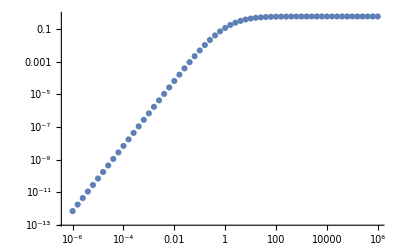

```mathematica
ListLogLogPlot[Evaluate@Table[ With[{x := 10^xp}, Table[{x,σTot[thing, x]}, {xp, -6, 6, 0.2}]], {thing, {d5}}]]
```

```mathematica
d1low[mx_]:= (mn^2*mx^2)/(2*π*(μ[mx]+1)^2);
d2low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(8*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2);
d3low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(8*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2);
d4low[cθ_,w_, mx_]:= (mn^2*μ[mx]^2)/(32*π*(μ[mx]+1)^2)*((1-cθ)*w^2*(2*mx^2)/(1+μ[mx])^2)^2;
d5low[cθ_,w_, mx_]:= mx^2/(2*π*(μ[mx]+1)^2);
```

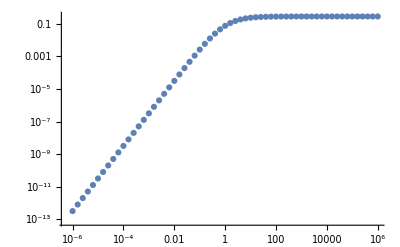

```mathematica
ListLogLogPlot[With[{x:=10^xp}, Table[{x, Integrate[d5low[y, 0.6, x], {y, -1,1}]}, {xp, -6, 6, 0.2}]]]
```

```mathematica
With[{x:=10^xp}, Table[{x, Integrate[d2low[y, 0., x], {y, -1,1}]}, {xp, -6, 6, 0.2}]]
```

{{1.×10^-6,0.},{1.58489×10^-6,0.},{2.51189×10^-6,0.},{3.98107×10^-6,0.},{6.30957×10^-6,0.},{0.00001,0.},{0.0000158489,0.},{0.0000251189,0.},{0.0000398107,0.},{0.0000630957,0.},{0.0001,0.},{0.000158489,0.},{0.000251189,0.},{0.000398107,0.},{0.000630957,0.},{0.001,0.},{0.00158489,0.},{0.00251189,0.},{0.00398107,0.},{0.00630957,0.},{0.01,0.},{0.0158489,0.},{0.0251189,0.},{0.0398107,0.},{0.0630957,0.},{0.1,0.},{0.158489,0.},{0.251189,0.},{0.398107,0.},{0.630957,0.},{1.,0.},{1.58489,0.},{2.51189,0.},{3.98107,0.},{6.30957,0.},{10.,0.},{15.8489,0.},{25.1189,0.},{39.8107,0.},{63.0957,0.},{100.,0.},{158.489,0.},{251.189,0.},{398.107,0.},{630.957,0.},{1000.,0.},{1584.89,0.},{2511.89,0.},{3981.07,0.},{6309.57,0.},{10000.,0.},{15848.9,0.},{25118.9,0.},{39810.7,0.},{63095.7,0.},{100000.,0.},{158489.,0.},{251189.,0.},{398107.,0.},{630957.,0.},{1.×10^6,0.}}

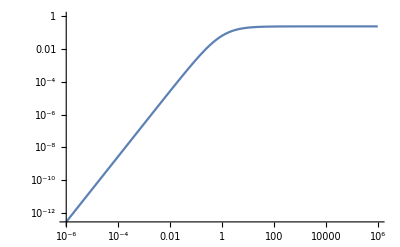

```mathematica
LogLogPlot[csd1low[x], {x, 10^-6, 10^6}]
```